```mathematica
5.33/(1.04/55.85*392.14)
```

0.729921

```mathematica
1.04/55.85*392.14
```

7.30216

```mathematica
0.1210/133.9985*2/5/0.01763
```

0.0204877

```mathematica
{#,Mean[#],MeanDeviation[#],MeanDeviation[#]/Mean[#]}&[#1/#2/133.9985*2/5*100&@@@{{0.1171,17.35},{0.1310,19.15},{0.1210,17.63}}]
```

{{0.00201473,0.00204203,0.00204877},0.00203518,0.0000136302,0.00669731}

```mathematica
list10=Transpose[{{0.1171,0.1310,0.1210},{17.35,19.15,17.63}}];
Mean[#1/134*2/5/(#2/1000)&@@@list10]
```

0.0203516

```mathematica
Mean[{17.05,17.08,17.05}*Mean[#1/134*2/5/(#2/1000)&@@@list10]/1000*25*392.14/3.5019]
```

0.971973

```mathematica
MeanDeviation[%5]/Mean[%5]
```

0.000781555

```mathematica
q=Tuples[{iA,iB,iO},2];
z=Transpose@{Tuples[q,2],Tuples/@Tuples[q,2]};
Examination[parents_,sons_]:=Tuples[parents,sons];
Test/@Flatten/@Tuples/@z
N[(Total@%)/Length[%]]
```

{0,1,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,0,0,1,1,1,1,0,0,1,0,0,0,1,0,1,1,1,0,1,0,1,1,1,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0}

0.617284

```mathematica
Test[list_]:=If[Count[list,iA]>0&&Count[list,iB]>0,1,0];
Test/@Flatten/@Tuples[First[z]]
```

{0,0,0,0,0,0,0,0}

```mathematica
\
```

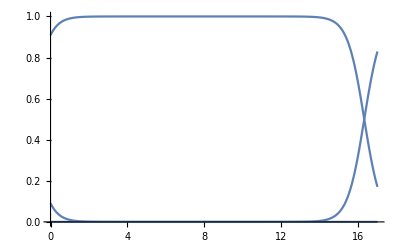

```mathematica
Plot[IonDistribution[10^-x,{10,4.86*10^-17}],{x,0,17}]
```

```mathematica
IonDistribution[10^(-(x-14)),{100,4.86*10^-17}]/.x->7
```

{0.99999,9.9999×10^-6,4.85995×10^-29}

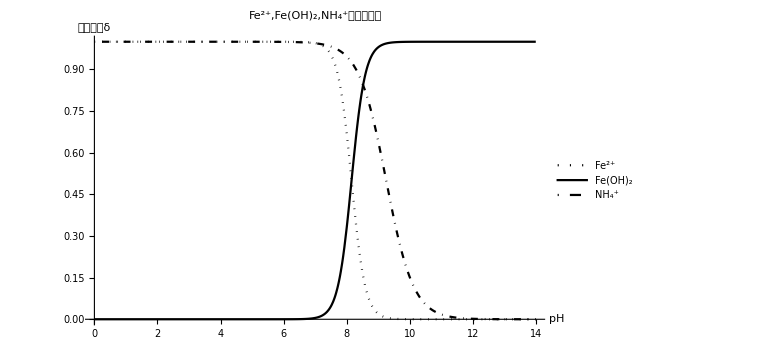

```mathematica
Plot[{((10^-x)^2)/((10^-x)^2+4.86*10^-17),1-((10^-x)^2)/((10^-x)^2+4.86*10^-17),10^-x/(10^-x+10^-14/(1.8*10^-5))},{x,0,14},PlotLegends->{"Fe^(2+)","Fe(OH)_2","NH_4^+"},PlotLabel->Style["Fe^(2+),Fe(OH)_2,NH_4^+分布系数图",Black,16],PlotStyle->{{Black,Dotted},{Black},{Black,DotDashed}},AxesLabel->{"pH","分布系数δ"},LabelStyle->Black,ImageSize->Large]
```

```mathematica
{((10^-x)^2)/((10^-x)^2+4.86*10^-17),1-((10^-x)^2)/((10^-x)^2+4.86*10^-17),10^-x/(10^-x+10^-14/(1.8*10^-5))}/.x->6
```

{0.999951,0.0000485976,0.999445}